### Convex Problems

#### Problems with unique optimal points

```mathematica
feasibleSet =ImplicitRegion[x^2≤ 2 && y^2 ≤ 1,{x,y}];
RegionPlot[feasibleSet]
```

-Graphics-

```mathematica
objective[x_,y_]:= x+y
sol = {x,y} /. NMinimize[objective[x,y], {x,y} ∈ feasibleSet][[2]]
```

{-1.41421,-0.999999}

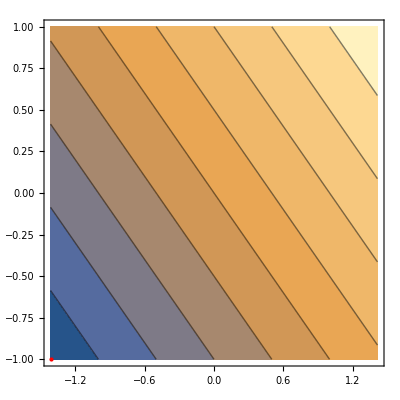

```mathematica
ContourPlot[x+y, {x,y} ∈feasibleSet,Epilog->{Red,PointSize[Large],Point[sol]}]
```

### Convex Problems

#### Problems with infinitely many optimal points

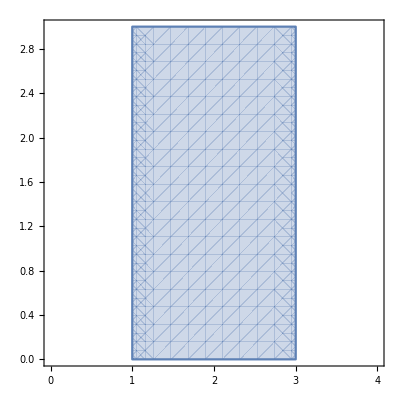

```mathematica
feasibleSet[x_,y_] :=(x-2)^2≤ 1 && y ≥ 0;
Ω = ImplicitRegion[feasibleSet[x,y],{x,y}];
RegionPlot[feasibleSet[x,y],{x,0,4},{y,0,3}]
```

```mathematica
objective[x_,y_]:= y
sol = {x,y} /. Minimize[objective[x,y], {x,y} ∈ Ω][[2]]
```

{2,0}

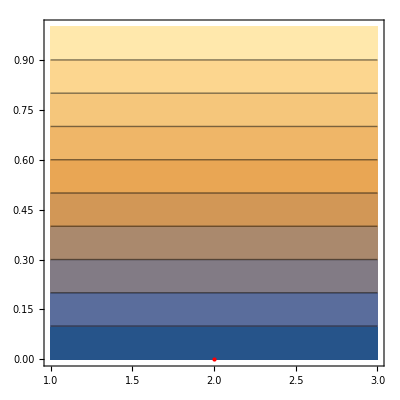

```mathematica
ContourPlot[objective[x,y], {x,y} ∈ Ω ,Epilog->{Red,PointSize[Large],Point[sol]}]
```

### Convex Problems

#### Problems with unbounded-below objectives

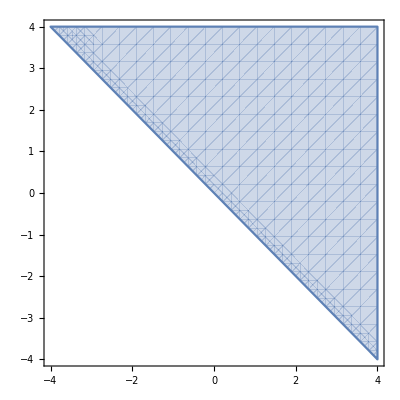

```mathematica
feasibleSet[x_,y_] := x + y ≥ 0;
Ω = ImplicitRegion[feasibleSet[x,y],{x,y}];
RegionPlot[feasibleSet[x,y],{x,-4,4},{y,-4,4}]
```

```mathematica
objective[x_,y_]:= x
sol = {x,y} /. NMinimize[objective[x,y], {x,y} ∈ Ω][[2]]
```

NMinimize::dinfeas: The dual is infeasible, which implies that the primal optimization is either unbounded or infeasible.

{Indeterminate,Indeterminate}

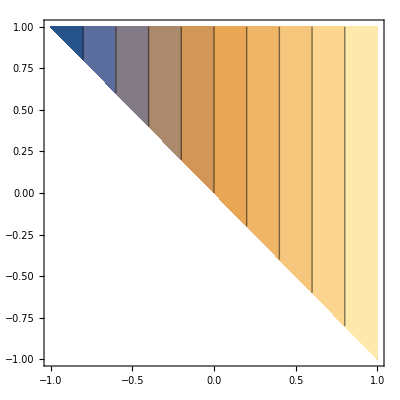

```mathematica
ContourPlot[objective[x,y], {x,y} ∈ Ω ]
```

### Convex Problems

#### Problems with open feasible sets

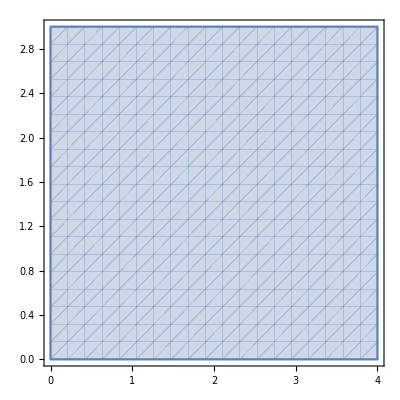

```mathematica
feasibleSet[x_,y_] :=x > 0;
Ω = ImplicitRegion[feasibleSet[x,y],{x,y}];
RegionPlot[feasibleSet[x,y],{x,0,4},{y,0,3}]
```

```mathematica
objective[x_,y_]:= (x+1)^2
sol = {x,y} /. Minimize[objective[x,y], {x,y} ∈ Ω][[2]]
```

Minimize::wksol: Warning: there is no minimum in the region in which the objective function is defined and the constraints are satisfied; returning a result on the boundary.

{0,0}

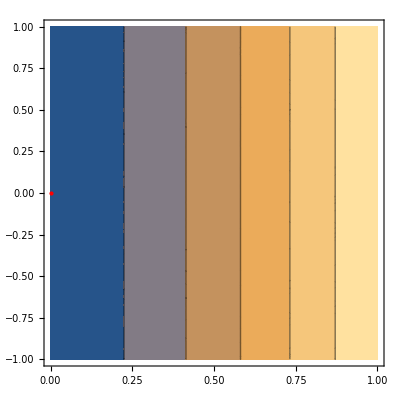

```mathematica
ContourPlot[objective[x,y], {x,y} ∈ Ω ,Epilog->{Red,PointSize[Large],Point[sol]}]
```

### Convex Problems

#### Problems with unfeasible sets

```mathematica
feasibleSet[x_,y_] := y ≥ (x-1)^2+1  && y-x + 1/2 ≤ 0;
Ω = ImplicitRegion[feasibleSet[x,y],{x,y}];
RegionPlot[feasibleSet[x,y],{x,-4,4},{y,-4,4}]
```

-Graphics-